# Soluciones periódicas

## Criterio de Dulac

## Ejemplo I:

Sea , entonces:

para toda  y  para toda .
Por lo tanto, no pueden haber soluciones periódicas completamente contenidas en alguna de las dos mitades del eje .

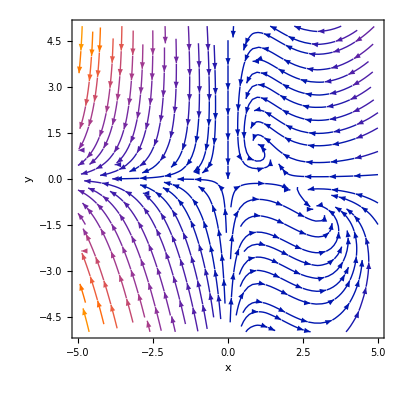

```mathematica
StreamPlot[{x*(2-x-y),y*(4*x-x^2-3)},{x,-5,5},{y,-5,5},FrameLabel->{x,y}]
```

## Ejemplo II:

Sea  entonces:

por lo tanto, no hay soluciones periódicas en ningún lugar de .

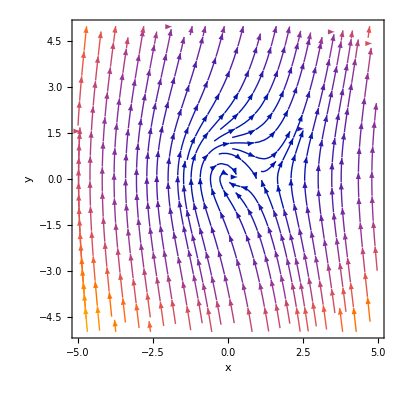

```mathematica
StreamPlot[{y,-x-y+x^2+y^2},{x,-5,5},{y,-5,5},FrameLabel->{x,y}]
```

## Teorema de Poincaré-Bendixson

## Ejemplo I:

Si  tenemos el ciclo límite bien acotado:

```mathematica
Manipulate[Show[{RegionPlot[1-m<x^2+y^2<1+m,{x,-2,2},{y,-2,2},FrameLabel->{x,y}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2)+m*r*Cos[θ],1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2)+m*r*Cos[θ],1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamPoints->{{0,1}},StreamColorFunction->None,StreamStyle->{Red,Thick},StreamMarkers->"Box"]}],{m,0.3,1}]
```

Si , el ciclo límite sigue existiendo pero el criterio anterior ya no sirve para demostrar que existe:

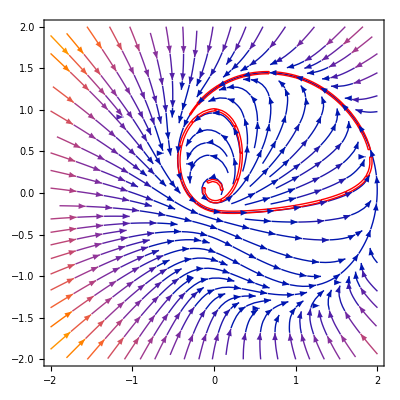

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2)+3*r*Cos[θ],1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2)+3*r*Cos[θ],1},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamPoints->{{0,1}},StreamColorFunction->None,StreamStyle->{Red,Thick},StreamMarkers->"Box"]}]
```